# Bayesian particle in a box

The particle in a box is usually the first real example that quantum mechanics students run into after the free particle, and it introduces the first actual quantization result. Here I will recreate the quantization result with a modified version of Bayesian probability, and hopefully this will somewhat demystify the ‘magic’ of quantum mechanics.

So is it possible? Can we extract physical results from probability?

## Bayesian free particle

First, let’s examine a free particle with unknown initial position and velocity.

We’ll start with a very simple physical model for a free particle in one dimension with no forces acting upon it. We’ll let x(t) be the particle’s position at time t.  Newton’s laws tell us that without any forces acting on the particle it will move along with a constant velocity forever. In differential equation terms we can say that x'(t)=v where v is the initial velocity of the particle. Solving this very simple differential equation gives us a closed form trajectory for the particle, given by x(t)=x(0)+v t. 

This means that we can entirely parametrize the particle’s trajectory with two variables: x(0) and v.

Suppose that now we are uncertain about the particles initial position and velocity, but we have some distribution for them. Suppose that the initial position and velocity are each independent, and that we have some prior normal distribution for them. By creating an ensemble of particles we can simulate how our distribution should evolve over time. Let’s call the initial mean and variance of position μ_xand σ_x, and the mean and variance of the velocity μ_vand σ_v.

Let’s create a function which generates trajectories given initial conditions.

```mathematica
x[x0_,v_][t_]:=x0+v t
```

And then we can generate an ensemble of particles to simulate how the distribution will change over time.

```mathematica
(*Make some distrubutions for x(0) and v*)
x0Dist[μx_,σx_]:=NormalDistribution[μx,σx];
vDist[μv_,σv_]:=NormalDistribution[μv,σv];
(*Some parameters for the distributions*)
μx=0;
σx=1;
μv=2;
σv=1;

(*generate the ensamble of tradjectories*)
ensamble=Array[
x[
RandomVariate[x0Dist[μx,σx]],
RandomVariate[vDist[μv,σv]]
]&
,10000];
(*function to evaluate the ensamble at time t*)
ensambleAt[t_]:=#[t]&/@ensamble

(*controls for the ensamble*)
ensControls=Manipulate[
{μx,σx,μv,σv}={μxl,σxl,μvl,σvl};
ensamble=Array[x[RandomVariate[x0Dist[μx,σx]],RandomVariate[vDist[μv,σv]]]&,5000];
{{"μ_x",μx},{"σ_x",σx},{"μ_v",μv},{"σ_v",σv}}//TableForm,
{{μxl,0,"μ_x"},-10,10},
{{σxl,1,"σ_x"},.1,5},
{{μvl,2,"μ_v"},-10,10},
{{σvl,1,"σ_v"},.1,5},
BaselinePosition->Top
];
(*controls for the simulation*)
simControls=Manipulate[
Dynamic[Histogram[
ensambleAt[t],{.5},"PDF",
PlotRange->{{-10,10},{0,1}},
AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large
]],
{t,0,10},
BaselinePosition->Top
];
Row[{ensControls,simControls}]
```

If you don’t have access to the manipulate for whatever reason, here are some time slices:

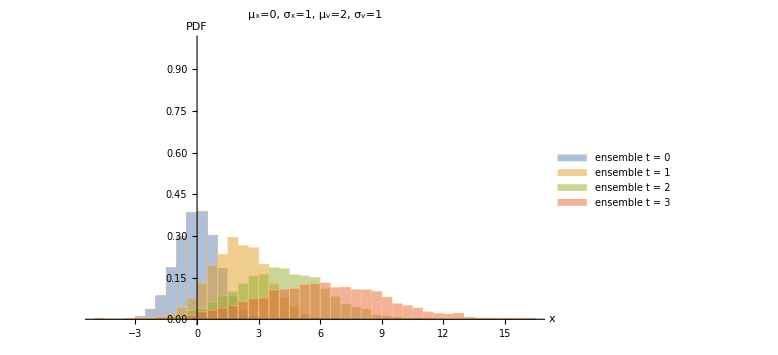

```mathematica
(*some styling that will make a future graphic better*)
colors=ColorData[97,"ColorList"];

ensambleSlices=Histogram[
Table[
ensambleAt[t],{t,{0,1,2,3}}
]//Evaluate,
{.5},"PDF",
PlotRange->{All,{0,1}},
AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large,
ChartLegends->Table["ensemble t = "<>ToString@t,{t,{0,1,2,3}}],
PlotLabel->"μ_x="<>ToString@μx<>", σ_x="<>ToString@σx<>", μ_v="<>ToString@μv<>", σ_v="<>ToString@σv,
ChartStyle->colors
]
```

This result makes a lot of sense. Overall the mean position is moving to the right, since the mean velocity is greater than zero. However, since there is some variance in the velocity, the distribution spreads out over time.

Numerical simulation is great for verification, but it is also somewhat slow and difficult to analyze rigorously. To generate an analytical solution, we need only think of the evolution of time as a continuous sequence of Bayesian updates.

To do this, we will have to account for all of our state variables. Even though velocity is constant in this example, it is not perfectly known, and must be thought of as a state variable. This means that we are looking for P(x,v|t), the probability of being at position x moving at velocity v at time t. The likelihoods are easy to calculate, since we can just run the simulation back to t=0 and sample the initial distribution. Let’s call ϕ(x,v) the initial distribution.

```mathematica
ϕ[μx_,σx_,μv_,σv_][x_,v_]:=PDF[x0Dist[μx,σx]][x]PDF[vDist[μv,σv]][v]
Like[μx_,σx_,μv_,σv_][xl_,v_,t_]:=ϕ[μx,σx,μv,σv][x[xl,v][-t],v]
Manipulate[
ContourPlot[
Quiet[Like[μx,σx,μv,σv][xl,v,t]],{xl,-10,10},{v,-10,10},
PlotRange->All,
PlotPoints->ControlActive[30,50],
MaxRecursion->ControlActive[0,1],
FrameLabel-> {x,v},
PlotLegends->Automatic,
PlotLabel->"Likelihoods at t="<>ToString@t
],
{{μx,0,"μ_x"},-10,10},
{{σx,1,"σ_x"},.1,5},
{{μv,2,"μ_v"},-10,10},
{{σv,1,"σ_v"},.1,5},
{t,0,3}
]
```

And of course, for those without Mathematica, we present some time slices:

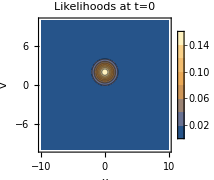
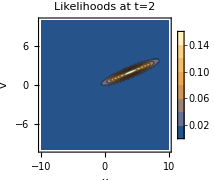
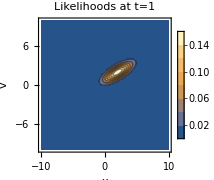
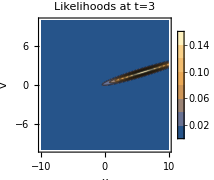
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Multicolumn@Table[
ContourPlot[
Quiet[Like[μx,σx,μv,σv][xl,v,t]],{xl,-10,10},{v,-10,10},
PlotRange->All,
FrameLabel-> {x,v},
PlotLegends->Automatic,
PlotPoints->50,
MaxRecursion->3,
PlotLabel->"Likelihoods at t="<>ToString@t,
ImageSize->Small
],
{t,{0,1,2,3}}]
```

Again, this makes sense. The fast parts move right faster, and the slow parts move right slower. Generally it looks like our distribution gets sheared along the diagonal.

We can then get the posterior probabilities by normalizing the data:

```mathematica
cacheVars:=cache={μx,σx,μv,σv};ClearAll[μx,σx,μv,σv];$Assumptions={xl∈Reals,v∈Reals,t>0,μx∈Reals,σx>0,μv∈Reals,σv>0};
uncacheVars:={μx,σx,μv,σv}=cache;
cacheVars;
Integrate[Like[μx,σx,μv,σv][xl,v,t],{xl,-∞,∞},{v,-∞,∞}]//Simplify
uncacheVars;
```

1

And wouldn’t you know, our system is inherently probability conserving! Isn’t that sweet. This means that our posterior probabilities are our likelihoods! Actually, we could have guessed this by looking at how the likelihoods evolve over time. Since shearing is area-conservative, it makes sense that the total likelihood is always equal to the original.

```mathematica
cacheVars;
Like[μx,σx,μv,σv][x,v,t]
uncacheVars;
```

(ⅇ^(-(v-μv)^2/(2 σv^2)-(-t v+x-μx)^2/(2 σx^2)))/(2 π σv σx)

So P(x,v|t)=(ⅇ^(-(v-μv)^2/(2 σv^2)-(-t v+x-μx)^2/(2 σx^2)))/(2 π σv σx).

And now, to get back to the pretty graphs from before, we can integrate out v to get the x marginal for the posterior.

```mathematica
cacheVars;
Integrate[Like[μx,σx,μv,σv][x,v,t],{v,-∞,∞}]//Simplify
uncacheVars;
```

(ⅇ^(-(-x+t μv+μx)^2/(2 (t^2 σv^2+σx^2))))/(√(2 π) √(t^2 σv^2+σx^2))

So P(x|t)=(ⅇ^(-(-x+t μv+μx)^2/(2 (t^2 σv^2+σx^2))))/(√(2 π) √(t^2 σv^2+σx^2)). With this result, we can make some more pretty animations and graphs of the probability distribution over time.

```mathematica
P[μx_,σx_,μv_,σv_][x_,t_]:=(ⅇ^(-(-x+t μv+μx)^2/(2 (t^2 σv^2+σx^2))))/(√(2 π) √(t^2 σv^2+σx^2))
Manipulate[
Plot[P[μx,σx,μv,σv][xl,t],{xl,-10,10},
PlotRange->{All,{0,1}},
Filling->Axis,AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large
],
{{μx,0,"μ_x"},-10,10},
{{σx,1,"σ_x"},.1,5},
{{μv,2,"μ_v"},-10,10},
{{σv,1,"σ_v"},.1,5},
{t,0,3}
]
```

And, once more for those who cannot drag the fancy sliders around, we present some time slices:

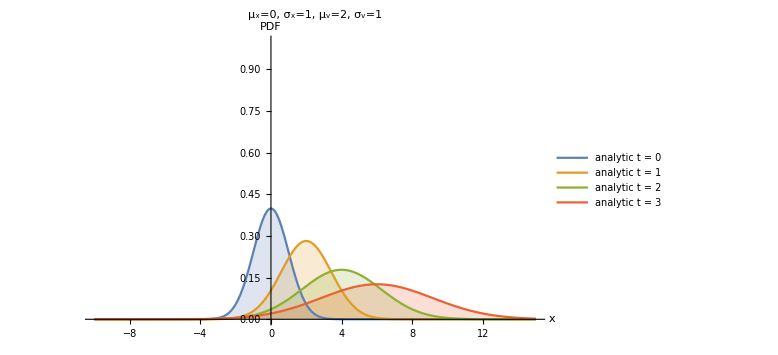

```mathematica
analyticSlices=Plot[Table[P[μx,σx,μv,σv][xl,t],{t,{0,1,2,3}}]//Evaluate,{xl,-10,15},
PlotRange->{All,{0,1}},
Filling->Axis,AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large,
PlotLegends->Table["analytic t = "<>ToString@t,{t,{0,1,2,3}}],
PlotLabel->"μ_x="<>ToString@μx<>", σ_x="<>ToString@σx<>", μ_v="<>ToString@μv<>", σ_v="<>ToString@σv
]
```

And for verification, we can look at both the analytic and ensemble models together:

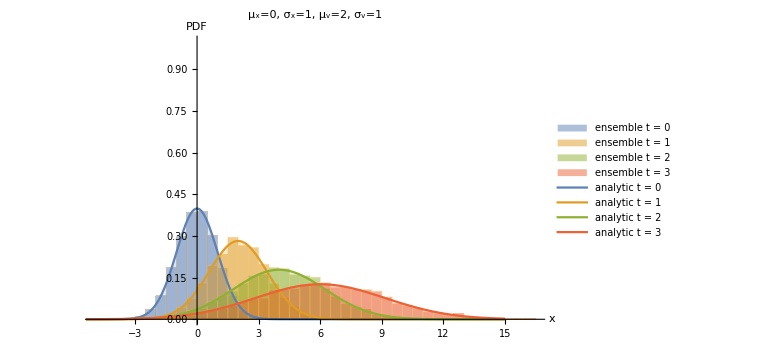

```mathematica
Show@{ensambleSlices,analyticSlices}
```

So yes, our analytic solution is correct!

We can even make a nice manipulate for the verification, to really drive the point home:

```mathematica
(*controls for the varification*)
varControls=Manipulate[
Dynamic[
Show@{
Plot[P[μx,σx,μv,σv][xl,t],{xl,-12,12},
PlotRange->{{-10,10},{0,1}},
Filling->Axis,AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large
],
Histogram[
ensambleAt[t],{.5},"PDF",
PlotRange->{{-10,10},{0,1}},
AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large,
ChartStyle->Directive[colors[[1]],Opacity[.1]]
]
}
],
{t,0,4},
BaselinePosition->Top
];
Row[{ensControls,varControls}]
```

This is all fine and dandy, and this behaviour does line up with what physicists predict for particles of unknown momentum. However, without a potential well there is no actual quantization, i.e. the particle can be in a continuum of states without restriction, instead of the discrete states that quantum mechanics is famous for predicting. For that, we will have to move into a box, and do the particle in a box example.

## ‘Bayesian’ particle in a box

In this example, we will attempt to model a particle in a one dimensional box, bouncing between the walls. We can model the position of a particle over time just bouncing between the walls as

```mathematica
xt[x0_,v0_][t_]:=TriangleWave[{0,1},(t v0-1/2+x0)/(2)]
vt[x0_,v0_][t_]:=v0 SquareWave[{-1,1},(t v0+x0)/(2)]

Manipulate[Plot[{xt[x0,v][t],vt[x0,v][t]},{t,0,10},ExclusionsStyle->Dotted,PlotRange->{-1,1},PlotLegends->{x,"v"},AxesLabel->{time,}],{{v,1},-1,1},{{x0,.5},0,1}]
```

Naively we might want to try to do the exact same thing with this example as we did in the last example. However, this time we actually have a destination in mind. Quantum mechanics predict quantized (discrete) steady state distributions of the form ψ_n(x)=2sin^2(n π x), where n is the ‘principle quantum number’ if you are feeling fancy, and is ‘any natural number’ if you aren’t.

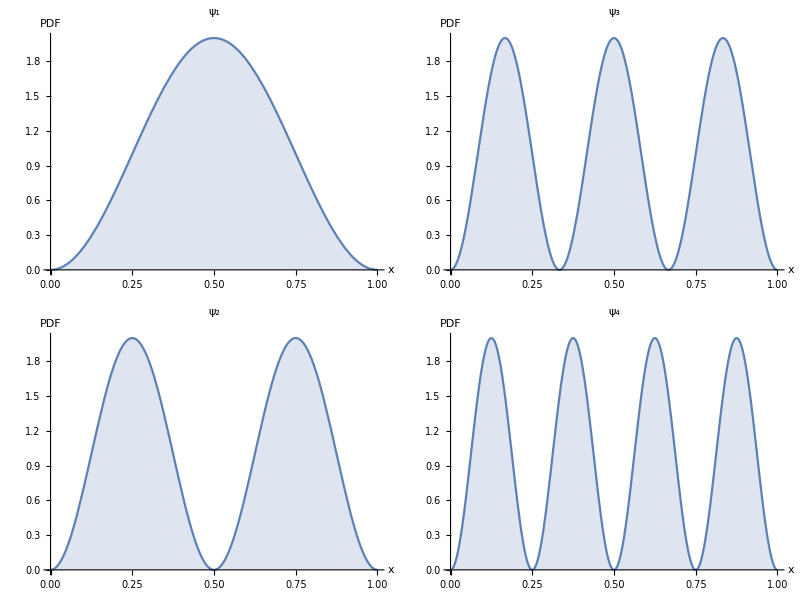

```mathematica
ψ[n_][x_]:=2Sin[n π x]^2
Multicolumn@Table[Plot[ψ[n][x],{x,0,1},PlotLabel->Subscript[ψ, n],Filling->Axis,AxesLabel->{x,PDF}],{n,1,4}]
```

And we can already identify an issue with the naive model from the last example. With any distribution of velocities besides ‘the particle definitely never moves’ these distributions cannot be constant over time. Even if we make it equally likely that the particle is moving left and right, we end up with this:

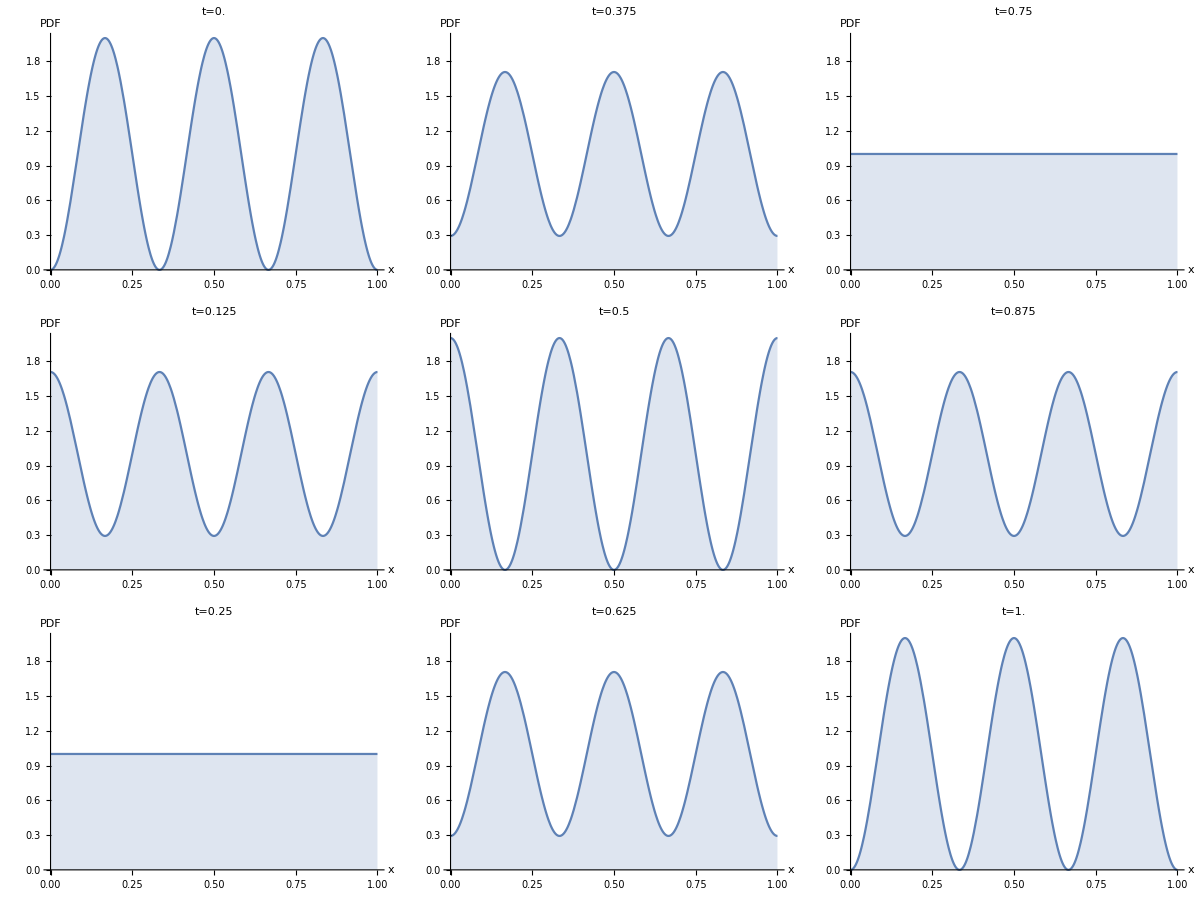

```mathematica
Manipulate[Plot[(ψ[3][x-t]+ψ[3][x+t])/2,{x,0,1},PlotLabel->"t="<>ToString@t,Filling->Bottom,PlotRange->{0,2},AxesLabel->{x,PDF}],{t,0,1}]
Multicolumn@Table[Plot[(ψ[3][x-t]+ψ[3][x+t])/2,{x,0,1},PlotLabel->"t="<>ToString@t,Filling->Bottom,PlotRange->{0,2},AxesLabel->{x,PDF}],{t,0,1,1/8//N}]
```

Which is clearly a standing wave, and not stationary.

However, all is not lost! It turns out that when defining likelihoods, at no point is it required that you define them as real numbers between zero and one. In fact, there is already a perfectly good definition of likelihood as odds, where they are between 1 and infinity. Here we will offer an interesting form for likelihoods: complex numbers! It becomes somewhat harder to extract traditional probabilities from complex probabilities, but it is possible. This is not an abstract algebra class, but the gist of it is that you can extract real probability by taking the magnitude squared of a complex probability.

Knowing this, we can construct an initial complex distribution of the particles initial position and velocity. For the sake of simplicity I’ll assume that the particle is a photon, so that the velocity is definitely either c or -c, since the photon is definitely only moving at the speed of light. We’ll define the initial complex probability distribution of the particle’s position and velocity with two functions, ψ_L(x) for the distribution of the particles with velocity -c, and ψ_R(x) for the distribution of particles with velocity c.

To actually find ψ_L(x) and ψ_R(x) we will work backwards from the answer that physics gives us.

For a stationary distribution, the way that the complex probability distribution evolves in time looks like this:

```mathematica
ParametricPlot3D[Table[param[x,Exp[I t /π]Sin[3π x]],{t,0,6,2}]//Evaluate,{x,0,1},AxesLabel->{"x",Im,Re},BoxRatios->{2, 1, 1},PlotLegends->Table["t="<>ToString@t,{t,0,3}]]
Manipulate[ParametricPlot3D[param[x,Exp[I t /π]Sin[3π x]],{x,0,1},AxesLabel->{"x",Im,Re},BoxRatios->{2, 1, 1},PlotRange->{All,{-1,1},{-1,1}}],{t,0,18}]
```

-Graphics3D-

That is, they evolve over time by just rotating through the complex plain. Remember that the real valued probability is  the complex probability’s magnitude squared, so they really area stationary in the traditional sense. Since they are rotating in the complex plain, they have real an imaginary parts which are standing waves. We know that standing waves can be generated by a sum of a wave traveling left and a wave traveling right, so we can find initial complex distributions for those waves and call them ψ_L(x) and ψ_R(x). It turns out that the form that works is ψ_L(x)=1/2 ι exp(-ι n π x) and ψ_R(x)=-1/2ι exp(ι n π x), which form a nice double helix.

```mathematica
ψL0[n_][x_]:=1/2 I Exp[-I n π x]
ψR0[n_][x_]:=-1/2 I Exp[I n π x]
param[x_,f_]:={x,Re[f],Im[f]}
ParametricPlot3D[{param[x,ψL0[3][x]],param[x,ψR0[3][x]]},{x,0,1},AxesLabel->{"x",Im,Re},BoxRatios->{2, 1, 1}]
```

-Graphics3D-

We can also plot the magnitude squared of those initial conditions to find the real valued initial position distribution given they we know the velocity is left or right.

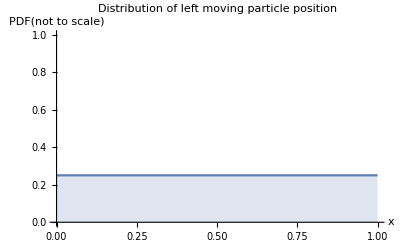

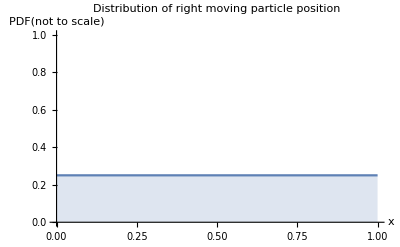

```mathematica
Plot[ψL0[2][x](ψL0[2][x])*,{x,0,1},PlotRange->{0,1},Filling->Bottom,PlotLabel->"Distribution of left moving particle position",AxesLabel->{x,"PDF(not to scale)"}]
Plot[ψR0[2][x](ψR0[2][x])*,{x,0,1},PlotRange->{0,1},Filling->Bottom,PlotLabel->"Distribution of right moving particle position",AxesLabel->{x,"PDF(not to scale)"}]
```

And we can see that these are actually twisted uniform distributions! A particle with a specific velocity has an equal chance of being anywhere. We will also be modeling the particle as having an equal initial chance of moving left or right, so these really are uniform distributions in most senses of the word, and it is not too hard to believe that they will be stationary, since every state is equally likely initially. 

The ‘weird quantum behavior’ emerges only when we add the left and right distributions. Since they aren’t real valued, they don’t add the way you would expect. Here’s that distribution:

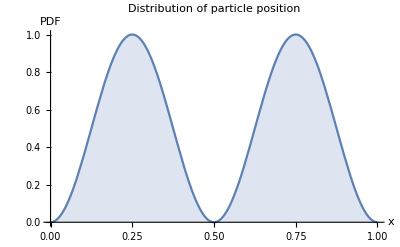

```mathematica
Plot[(ψR0[2][x]+ψL0[2][x])(ψR0[2][x]+ψL0[2][x])*,{x,0,1},PlotRange->{0,1},Filling->Bottom,PlotLabel->"Distribution of particle position",AxesLabel->{x,PDF}]
```

This is (unsurprisingly) one of the stationary distributions.

Finally there is one more thing we need. In order for the standing waves to work in our bouncing model, we need for the ‘phase’ of the particle to get negated each time it hits the wall and bounces off. This amounts to multiplying the probability by -1, which does not effect the magnitude of the probability, so it does not effect the real valued probability. This may seem nonphysical, but it actually does happen in nature. When light reflects off a mirror, its phase is increased by π, which is equivalent to a 180° rotation, or multiplying a complex number by -1.

If you really want to, you could think of this as saying that the photon has a likelihood of -1 of bouncing off the wall (i.e. it definitely will, but don’t expect it’s likelihood afterwards to add the same way it did before)

Also, this is mostly an artifact of a glaring issue with this model: particles don’t really bounce instantly. This model assumes an infinite potential energy outside of the box, which is pretty much nonphysical. I think that this correction is adjusting for that.

All together, we can now create our ‘Bayesian’ (complex Bayesian) model:

```mathematica
(*reflection phase parameter: either multiply the phase by 1 if we have bounced*)
(*an even number of times, or -1 for an odd number of times*)
ϕt[x0_,v0_][t_]:=SquareWave[{-1,1},(t v0+x0)/2]

(*initially the particle has an equal chance of moving left or right*)
(*so to find future distributions we add the contribution of each of those cases*)
ψL[n_][x_,t_]:=With[{x0=xt[x,-1][-t],v0=vt[x,-1][-t]},
ϕt[x0,v0][t]*If[v0==-1,ψL0,ψR0][n][x0]
]
ψR[n_][x_,t_]:=With[{x0=xt[x,1][-t],v0=vt[x,1][-t]},
ϕt[x0,v0][t]*If[v0==-1,ψL0,ψR0][n][x0]
]
ψ[n_][x_,t_]:=ψL[n][x,t]+ψR[n][x,t]
```

If you don’t have Mathematica I highly encourage you to download it here, because this next animation is great.

I never coded anything about the frequency of the oscillation of ψ through the complex plain; it is entirely emergent. Nevertheless, they stationary distributions with higher values for n oscillate faster by moving at the same speed, just like light does in real life!

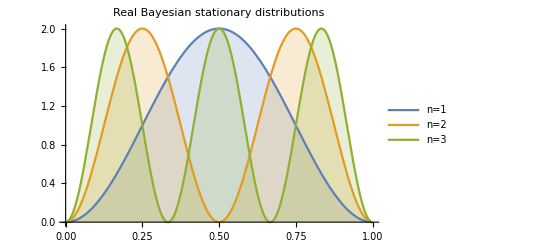

```mathematica
Manipulate[ParametricPlot3D[Table[param[x,ψ[n][x,t]],{n,1,3}]//Evaluate,{x,0,1},AxesLabel->{x,Re,Im},PlotRange->{All,{-1,1},{-1,1}},BoxRatios->{3, 1, 1},PlotLegends->Table["n="<>ToString@n,{n,1,3}],PlotLabel->"Complex Bayesian stationary distributions"],{t,0,5}]
Plot[Table[2ψ[n][x,0]ψ[n][x,0]*,{n,1,3}]//Evaluate,{x,0,1},Filling->Axis,PlotLegends->Table["n="<>ToString@n,{n,1,3}],PlotLabel->"Real Bayesian stationary distributions"]
```

## Discussion

It’s hard to get too far in the field of probability and statistics without encountering some kind of philosophical dilemma. Frequentist and Bayesian statistics offer different interpretations of what probabilities represent, and here I’ve offered a different interpretation of how probabilities add and multiply. When physicists were first realizing that physics is not deterministic, they were somewhat disgruntled. Some of the best experiments to date came from people sure they could prove quantum theory wrong, and some of the best Nobel prizes came from those experiments proving it right.

In the same way, it is tempting to entirely dismiss the idea of complex probability as some mathematical nonsense. One of the harder lessons of the last century of advances in physics, data science, and computer science is that no matter how nonsensical or pointless the math seems, it again and again turns out to describe reality or to be useful.

When studying the nature of probability, be thankful to live in a nondeterministic universe, where an experiment can point you in the direction of a proof.



That said, I can try to offer some rational for the complex probabilities, but it will be hand-wavy. 

In the free particle example, the time evolution of the distribution looks just like the heat equation (if the mean velocity is zero, that is). However, the heat equation is a first order differential equation, whereas Newton’s laws are second order. We’re pretty sure at this point that differential equations that describe reality are all second order.

The heat equation looks like this: ψ_t=k ψ_xx, where ψ_t is the partial derivative of ψ(x,t) with respect to time, ψ_xx is second partial derivative with respect to space, and k is just a proportionality constant.

The Schrödinger equation looks like this ψ_t=i k ψ_xx. It looks just like the heat equation, but with an imaginary unit i multiplying the right hand side. This actually makes it a system of two first order differential equations, which forms a second order differential equation, which happens to be isomorphic to the wave equation ψ_tt=k ψ_xx. 

Similarly, when we used complex probabilities we got wave-like behavior from the particle in a box. My theory is that the complex probabilities are simply the way to reconcile the heat-like behavior of Bayesian time evolution with the second order nature of reality, in much the same way that they can make a heat-like system behave like a wave-like system.